```mathematica
<<peeters`;
peeters`setGitDir["../project/figures/blogit"];

<<MaTeX`

(*See MathematicaColorToLatexRGB.nb for color mapping logic.*)
SetOptions[MaTeX,"Preamble"->{"\\usepackage{xcolor,txfonts}","\\definecolor{BlueDarker}{HTML}{0000AA}","\\definecolor{RedDarker}{HTML}{AA0000}","\\definecolor{PurpleDarker}{HTML}{550055}","\\definecolor{OrangeDarker}{HTML}{AA5500}","\\definecolor{GreenDarker}{HTML}{00AA00}"},
"FontSize" -> 16];
```

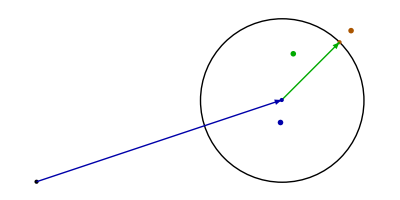

```mathematica
ClearAll[o, e1, e2, x, n, xp, dx, neighborhoodOfXFig7]
{e1, e2} = IdentityMatrix[2];
o = 0 e1;
x = 3 e1 + e2;
xp = x + (e1 + e2)/Sqrt[2];
dx = xp - x;
n[d_] := Module[{c},
c = d[[1]] + I d[[2]];
c = I c;
{c // Re, c //Im} // Normalize
]

neighborhoodOfXFig7 = Graphics[{
PointSize -> Large,
Thick,
Point[o],

Circle[x, 1],

Orange// Darker,
Point[xp],
Text[MaTeX["\\color{OrangeDarker}\\mathbf{x}'"], o + xp  + 0.2 Normalize[xp - x]],

Green//Darker,
Arrow[{o+x, xp}],
Text[MaTeX["\\color{GreenDarker}\\mathbf{x}' - \\mathbf{x}"], o + x  + 0.5 dx + 0.3 n[dx]],

Blue // Darker,
Point[x],
Arrow[{o,x}],
Text[MaTeX["\\color{BlueDarker}\\mathbf{x}"], o + x -0.25 n[x] - 0.1 Normalize[x]]
}]
```

```mathematica
peeters`exportForLatex["neighborhoodOfXFig7",neighborhoodOfXFig7]
```

{neighborhoodOfXFig7.eps,neighborhoodOfXFig7pn.png}